# David Meretzky Helmholtz

```mathematica
(*Geometry*)
```

```mathematica
nodes = {};
elements = {};
columns = 
n = 0;
For[i = 0, i ≤20,  i++, 
For[j =0, j ≤ 10, j++, 
n++;
node = {};
AppendTo[node, n];
AppendTo[node,i];
AppendTo[node, Mod[j,11]];
AppendTo[nodes,node];
];
];


n = 0;
For[i = 0, i ≤ 19, i++, 
For[k = 1, k ≤ 10, k++, 
For[j = 1, j ≤ 2,j ++, 
n++;
element = {};

AppendTo[element, n];

If[OddQ[j], 
AppendTo[element, (i*11)+k];
AppendTo[element,(i*11)+k + 11]; 
AppendTo[element, (i*11)+k + 12]; 
];

If[EvenQ[j], 
AppendTo[element,(i*11)+k];
AppendTo[element, (i*11)+k+12]; 
AppendTo[element, (i*11)+k+1]; 
];

AppendTo[elements, element];

];
];
];
```

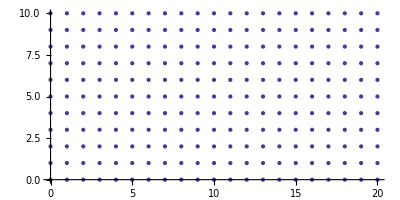

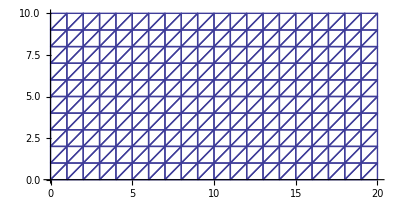

```mathematica
el= {};
For[i = 1, i ≤ Length[elements], i++,


node = nodes[[elements[[i,2;;4]],2;;3]];
 AppendTo[node,nodes[[elements[[i,2;;4]],2;;3]][[1]]];
AppendTo[el,node];
];

ListPlot[nodes[[1;;Length[nodes],2;;3]], AspectRatio->Automatic]
ListLinePlot[el, PlotStyle->Hue[.67, .6, .6], AspectRatio->Automatic]
```

## Formation of Vandermond Matrix and Polynomails

```mathematica
vand = {{1,0,0},{1,1,0},{1,0,1}};
units = {{1,0,0},{0,1,0},{0,0,1}};
MatrixForm[vand];

pol1[x_ , y_] :=LinearSolve[vand, units[[1]]].{1,x,y};
pol2[x_ , y_] :=LinearSolve[vand, units[[2]]].{1,x,y};
pol3[x_ , y_] :=LinearSolve[vand, units[[3]]].{1,x,y};

polys = {pol1,pol2,pol3};

grads = {{D[pol1[x,y],x],D[pol1[x,y],y]},
{D[pol2[x,y],x],D[pol2[x,y],y]},
{D[pol3[x,y],x],D[pol3[x,y],y]}};

Φ[x_, y_] := {.25*(1+x)*(1-y),.5*(1+y)};
```

## Analysis, K and M matricies

```mathematica
knByn = 0 *IdentityMatrix[Length[nodes]];
mnByn = 0 *IdentityMatrix[Length[nodes]];
For[i = 1, i ≤ Length[elements], ++i, 
coords = {{α,β},{γ,δ},{μ,ν}} = nodes[[elements[[i,2;;4]],2;;3]];

element = elements[[i]];

jacobianMatrix = Abs[Det[{{γ-α,μ-α},{δ-β,ν-β}}]];

xpts = {-1/Sqrt[3],1/Sqrt[3]};
ypts = {-1/Sqrt[3],1/Sqrt[3]};

For[j = 1, j ≤ 3,j++, 
nj = element[[2;;4]][[j]];
For[k = 1, k ≤ 3, k++,
nk = element[[2;;4]][[k]];

knByn[[nj,nk]] +=(1/8)*∑_(l=1)^2 ∑_(m=1)^2 (grads[[j]].grads[[k]])*jacobianMatrix;

mnByn[[nj,nk]] +=(1/8)*∑_(l=1)^2 ∑_(m=1)^2 polys[[j]][Φ[xpts[[l]],ypts[[m]]][[1]],Φ[xpts[[l]],ypts[[m]]][[2]]]*polys[[k]][Φ[xpts[[l]],ypts[[m]]][[1]],Φ[xpts[[l]],ypts[[m]]][[2]]]
*jacobianMatrix     (* end of summation *)


];   (* end of first iterator over polynomial gradients *)

];   (* end of second iterator over polynomial gradients *)
];  (* end of iterator over elements*)
```

## Dirichlet Boundary Conditions

```mathematica
uvect=ConstantArray[0,231];

uvect[[1]] = 1;

knByn[[1]]=uvect;
mnByn[[1]]=uvect;
```

## Solving the Eigensystem

```mathematica
invmnByn=-Inverse[mnByn];
eigenVectors = Eigenvectors[knByn.invmnByn]
```

{{0.,7.94226×10^-10,-1.89829×10^-9,1.44722×10^-9,-7.32856×10^-10,2.85082×10^-10,«220»,-0.0000656212,-0.0000268922,0.0000132342,-2.77913×10^-6,-4.71403×10^-8},«229»,{0.,«229»,-«19»}}

```mathematica
eigenVectors = Eigenvectors[{knByn, mnByn}]
```

{{0.,1.15243×10^-9,-1.73691×10^-9,1.19286×10^-9,-5.71547×10^-10,2.13233×10^-10,-6.33558×10^-11,1.42642×10^-11,-1.82093×10^-12,-2.72033×10^-13,2.60459×10^-13,-1.41026×10^-9,-7.45727×10^-9,4.95711×10^-9,-1.96788×10^-9,5.26528×10^-10,-6.89325×10^-11,-1.99152×10^-11,1.81486×10^-11,-7.75946×10^-12,2.38931×10^-12,-5.81922×10^-13,-1.17893×10^-7,5.93891×10^-8,«184»,-2.53969×10^-8,0.672614,-0.037421,-0.0188481,0.00718074,-0.00111013,-0.0000750319,0.0000930016,-0.0000264113,3.00872×10^-6,6.83985×10^-7,-4.48211×10^-7,-0.504143,-0.191418,0.057555,-0.00452093,-0.00198846,0.000879338,-0.000157885,-3.71059×10^-6,0.0000114009,-3.64723×10^-6,5.34351×10^-7},«229»,{0.,«229»,«20»}}

## Post Processing making final polynomials

```mathematica
frames = {};

For[j = 1, j ≤ 231, ++j, 
frame = {};
For[i = 1, i ≤ 400, i ++, 




If[OddQ[i],
centerx = nodes[[elements[[i,2;;4]],2;;3]][[1,1]] + .7;
centery = nodes[[elements[[i,2;;4]],2;;3]][[1,2]] + .3;
];
If[EvenQ[i],
centerx = nodes[[elements[[i,2;;4]],2;;3]][[1,1]] + .3;
centery = nodes[[elements[[i,2;;4]],2;;3]][[1,2]] + .7;
];

polys = {pol1[centerx,centery], pol2[centerx,centery],pol3[centerx,centery]};

polynomial = 
eigenVectors[[j,elements[[i,2]]]]*polys[[1]]+
eigenVectors[[j,elements[[i,3]]]]*polys[[2]]+
eigenVectors[[j,elements[[i,4]]]]*polys[[3]];


AppendTo[frame,{centerx,centery,polynomial}];
];
AppendTo[frames, frame];
];
```

```mathematica
Length[centerx]
```

231

## Visualization

```mathematica
ListPlot3D[frames[[1]], PlotRange->All]
ListPlot3D[frames[[20]], PlotRange->All]
ListPlot3D[frames[[40]], PlotRange->All]
ListPlot3D[frames[[100]], PlotRange->All]
ListPlot3D[frames[[200]], PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»